# ЛАБОРАТОРНАЯ РАБОТА 1. ГАММА-ФУНКЦИЯ

Выполнил студент ММФ БГУ
КМ, 1 к, 5 гр. Плисюк Г.С.
8 сентября 2021
Вариант 9

## 2. Знакомство с Гамма-функцией

### Задание 2.1

Отыщите информацию о Гамма-функции в системе справки Mathematica.

```mathematica
?Gamma
```

### Задание 2.2

Постройте график Гамма-функции.

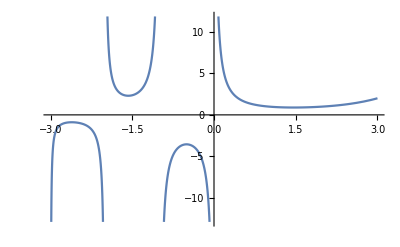

```mathematica
Plot[Gamma[x],{x,-3,3}]
```

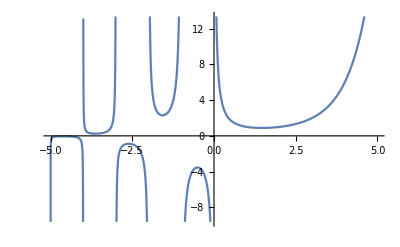

```mathematica
Plot[Gamma[x],{x,-5,5}]
```

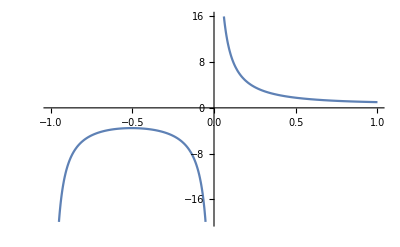

```mathematica
Plot[Gamma[x],{x,-1,1}]
```

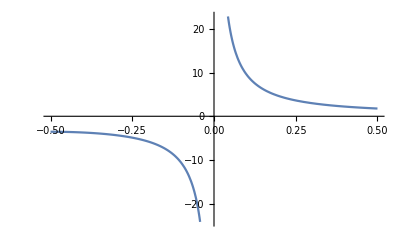

```mathematica
Plot[Gamma[x],{x,-0.5,0.5}]
```

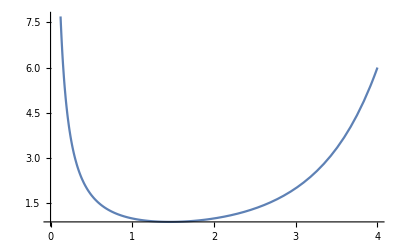

```mathematica
Plot[Gamma[x],{x,0,4}]
```

## 3. Сравнение Гамма-функции с известными функциями

### Задание 3.1

Полюбопытствуйте, какие значения принимает Гамма-функция на множестве натуральных чисел.

```mathematica
Gamma/@{1,2,3,4,5,6,7}
```

{1,1,2,6,24,120,720}

```mathematica
Range[4]
```

{1,2,3,4}

```mathematica
Range[4,7]
```

{4,5,6,7}

```mathematica
Range[4, 7, 0.5]
```

{4.,4.5,5.,5.5,6.,6.5,7.}

Функция Range, вызванная с 1 аргументом, образует список натуральных чисел от 1 до значения, переданного этим аргументом. Если аргументов 2, то создаётся список натуральных чисел от значения первого до значения второго аргументов; а если 3 -  то третьим аргументом задаётся шаг между элементами списка.

```mathematica
Gamma/@Range[7]
```

{1,1,2,6,24,120,720}

Композиция функций вычисляется поэтапно от низшего уровня выражения до нулевого. Т. е. перед вычислением значения каждой функции

Значение Гамма-функции для натуральных n совпадает со значениями выражения (n-1)!.

### Задание 3.2

Сравните значения функций Гамма и Факториал.

```mathematica
Factorial/@{1,2,3,4,5,6,7}
```

{1,2,6,24,120,720,5040}

```mathematica
Gamma[#+1]&/@{1,2,3,4,5,6,7}
```

{1,2,6,24,120,720,5040}

Γ(n+1)=n!, где n∈ℕ.

```mathematica
Gamma[#+1]-Factorial[#]&/@Range[7]
```

{0,0,0,0,0,0,0}

Поскольку Γ(n+1)=n!, где n∈ℕ, то значение выражения Γ(n+1) - n! = 0, для ∀n∈ℕ.

```mathematica
Gamma[#+1]-Factorial[#]&/@Range[70]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Описанная мною с помощью символа & анонимная функция вызывается для каждого элемента списка аргументов, для чего используется функция Map, записанная с помощью её алиаса вида /@. Аргумент в теле анонимной функции описывается через #.

### Задание 3.3

Постройте график дискретной функции Факториал двумя способами. В каждом случае используйте встроенную функцию ListPlot.

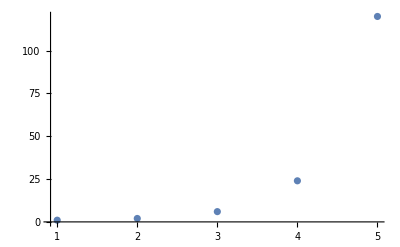

```mathematica
ListPlot[{#,#!}&/@Range[5]]
```

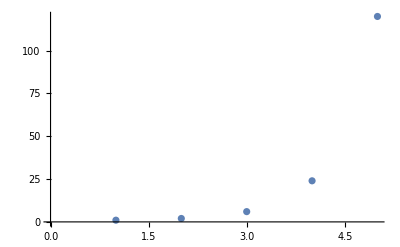

```mathematica
ListPlot[Table[n!,{n,1,5}]]
```

```mathematica
Table[x^3,{x,4}]
```

{1,8,27,64}

```mathematica
Table[h,3]
```

{h,h,h}

```mathematica
Table[10i+j,{i,3},{j,4}]
```

{{11,12,13,14},{21,22,23,24},{31,32,33,34}}

Функция Table генерирует список значений выражения, переданного первым аргументом, подставляя в него вместо символа, указанного первым элементом списка, переданного вторым аргументом, значения от второго до третьего элементов этого списка.

### Задание 3.4

Постройте одной и той же системе координат графики Гамма-функции и известных Вам элементарных функций: квадратичной, кубической, экспоненты ⅇ^x.

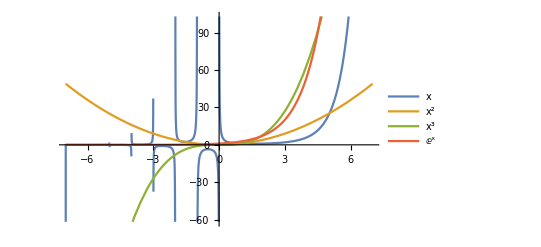

```mathematica
Plot[{Gamma[x],x^2,x^3,ⅇ^x},{x,-7,7},PlotLegends->"Expressions"]
```

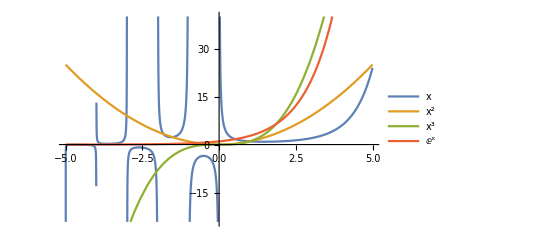

```mathematica
Plot[{Gamma[x],x^2,x^3,ⅇ^x},{x,-5,5},PlotLegends->"Expressions"]
```

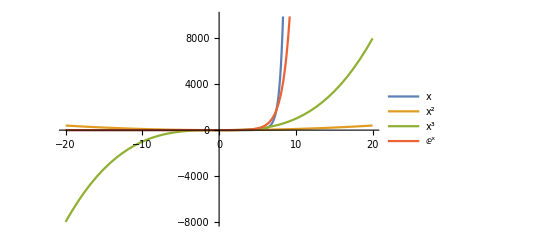

```mathematica
Plot[{Gamma[x],x^2,x^3,ⅇ^x},{x,-20,20},PlotLegends->"Expressions"]
```

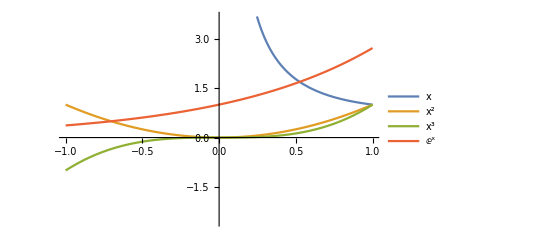

```mathematica
Plot[{Gamma[x],x^2,x^3,ⅇ^x},{x,-1,1},PlotLegends->"Expressions"]
```

На мой взгляд, отрезок (-7;7) более всего подходит для сравнения поведения функций, так как на нём видна симметрия, показаны значения для положительных и отрицательных аргументов, можно сопоставить скорости роста функций, а также их изменение.

### Задание 3.5

Сравните поведение Гамма-функции и известных Вам элементарных функций: квадратичной, кубической, экспоненты ⅇ^x.

```mathematica
Log/@ {Gamma[x],x^10,ⅇ^x}
```

{Log[Gamma[x]],Log[x^10],Log[ⅇ^x]}

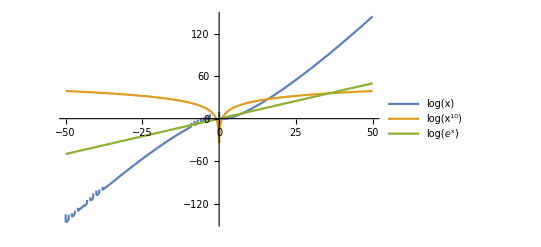

```mathematica
Plot[{Log[Gamma[x]],Log[x^10],Log[ⅇ^x]},{x,-50,50},PlotLegends->"Expressions"]
```

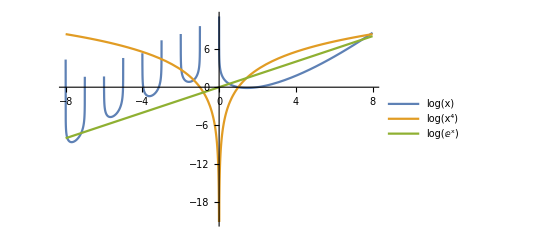

```mathematica
Plot[{Log[Gamma[x]],Log[x^4],Log[ⅇ^x]},{x,-8,8},PlotLegends->"Expressions"]
```

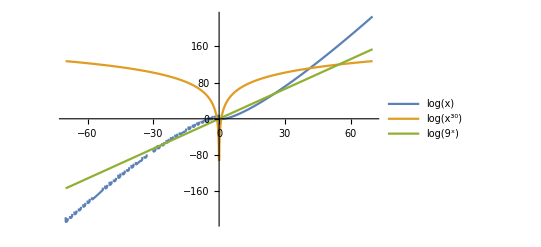

```mathematica
Plot[{Log[Gamma[x]],Log[x^30],Log[9^x]},{x,-70,70},PlotLegends->"Expressions"]
```

Гамма-функция растёт быстрее, чем любая другая использованная мною функция после определённого “критического” значения аргумента, которое тем больше, чем больше основание и показатель степени показательной и степенной функций.

Начиная со значения аргумента 1.5 Гамма-функция непрерывно растёт, при прибижении x к 0 значение функции стремится к бесконечности. На промежутке x<0 представляет собой чередующиеся положительные и отрицательные параболы, ограниченные целыми отрицательными аргументами и 0, для которых значение функции неопределенно.

## 4. Свойства известных функций и наша креативность

### Задание 4.1

Найдите рекуррентную формулу для вычисления значений Гамма-функции.

```mathematica
Plot[ⅇ^(x+1)/ⅇ^x,{x, -10, 10}]
```

-Graphics-

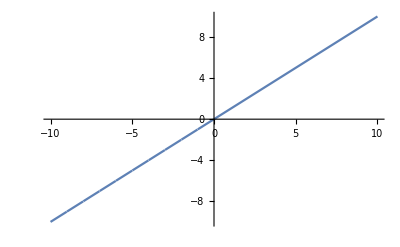

```mathematica
Plot[Gamma[x+1]/Gamma[x],{x, -10, 10}]
```

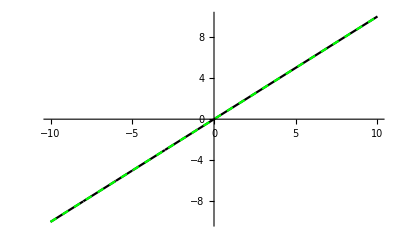

```mathematica
Plot[{Gamma[x+1]/Gamma[x],x},{x, -10, 10},PlotStyle->{Black,{Green,Dashed}}]
```

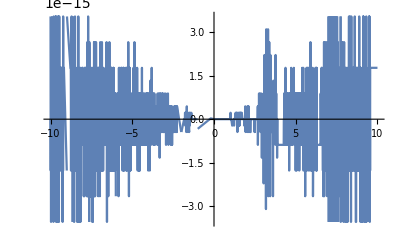

```mathematica
Plot[x-Gamma[x+1]/Gamma[x],{x, -10, 10}]
```

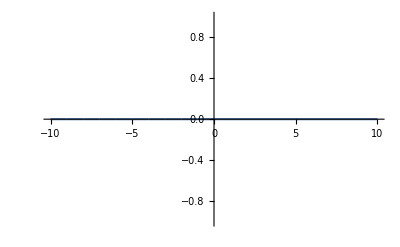

```mathematica
Plot[Round[x-Gamma[x+1]/Gamma[x]],{x, -10, 10}]
```

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

Рекуррентная формула для Гамма-функции: Γ(x+1)=x*Γ(x).

### Задание 4.2

Получите свойство Гамма-функции, которое описывает ее связь с гармоническими колебаниями.

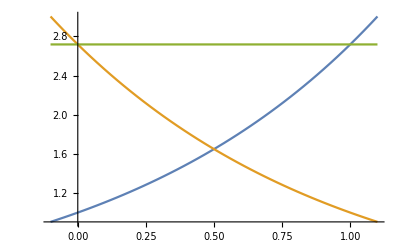

```mathematica
Plot[{ⅇ^x,ⅇ^(1-x),ⅇ^x ⅇ^(1-x)},{x, -0.1, 1.1}]
```

Полученные кривые симметричны относительно оси x=1/2.

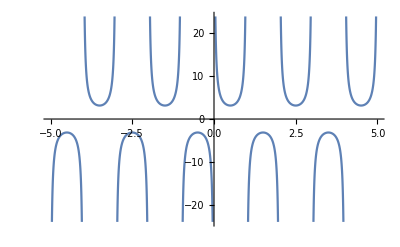

```mathematica
Plot[Gamma[1-x] Gamma[x],{x, -5, 5}]
```

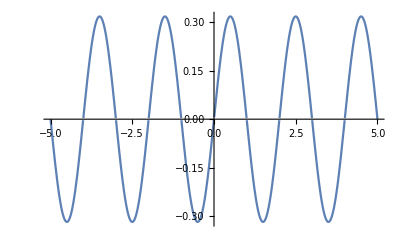

```mathematica
Plot[1/(Gamma[1-x] Gamma[x]),{x, -5, 5}]
```

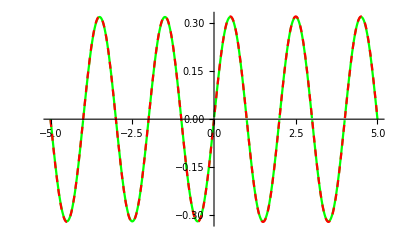

```mathematica
Plot[{1/(Gamma[1-x] Gamma[x]),0.32 Sin[3.14x]},{x, -5, 5}, PlotStyle->{Green,{Red,Dashed}}]
```

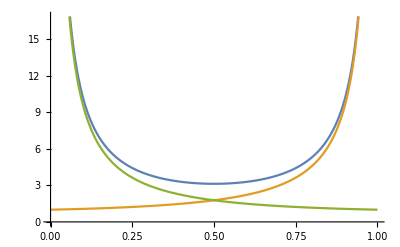

```mathematica
Plot[{1/(0.32 Sin[3.14x]),Gamma[1-x],Gamma[x]},{x, 0, 1}]
```

Подобное зеркальное отражение может быть полезно для упрощения нахождения значений гамма-функции на отрезке от [0;1], так как благодаря зависимости Γ(1-x)Γ(x) = π/(sin(πx)), если известно значение для Γ(1-x), то можно найти значение для Γ(x), и наоборот, если известно значение для Γ(x), то можно найти значение для Γ(1-x).

### Задание 4.3

Сформулируйте те свойства Гамма-функции, которые Вы получили при проведении исследований.

Значения Гамма-функции для натуральных чисел связано со значениями функции Факториал следующим выражением: Γ(n+1)=n!, где n∈ℕ. Из этого следует, что рекуррентная форма записи Гамма-функции выглядит следующим образом: Γ(n+1)=n*Γ(n).
	Гамма-функция растёт быстрее, чем любая показательная или степенная функция после определённого “критического” значения аргумента, которое тем больше, чем больше основание и показатель степени показательной и степенной функций.
	На промежутке n<0 представляет собой чередующиеся положительные и отрицательные параболы, ограниченные целыми отрицательными аргументами и 0, для которых значение функции неопределенно. На промежутке (0;1.5] функция убывает до значения 0.89, при этом при уменьшении аргумента до 0 значение функции стремится к бесконечности. Начиная со значения аргумента 1.5 Гамма-функция непрерывно растёт. 
	Нахождение значений Гамма-функции на отрезке от [0;1] можно облегчить с помощью зависимости Γ(1-x)Γ(x) = π/(sin(πx)), так как, если известно значение для Γ(1-x), то можно найти значение для Γ(x), и наоборот, если известно значение для Γ(x), то можно найти значение для Γ(1-x).